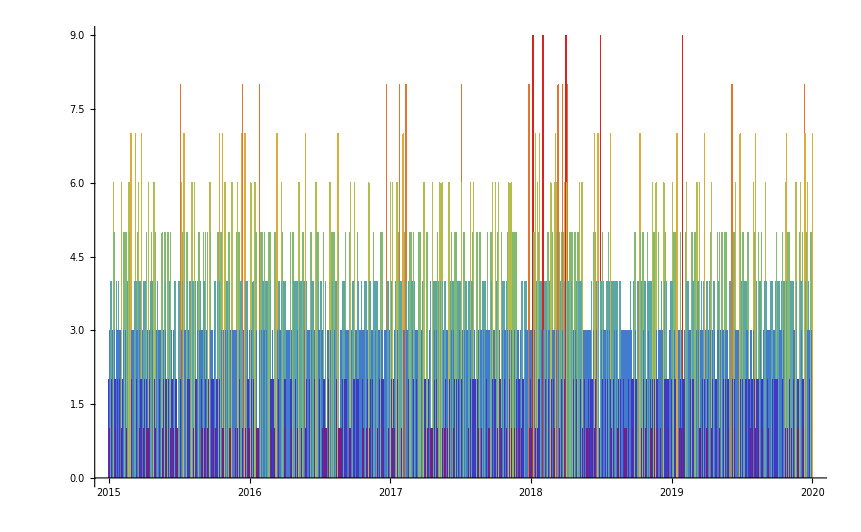

```mathematica
dataDates = Import["E:\\Course\\20Spring\\VE401\\proj2\\shootingdata.csv","Data"][[2;;4939,3]] ; 
DateHistogram[dataDates,"Day",ColorFunction->"Rainbow",DateTicksFormat->{" ", " ", "Year"}] (*For question 2*)
```

```mathematica
(*Tally is used to count repetitive terms*)
ShootingPerDay = Tally[dataDates];
count = Tally[ShootingPerDay[[All,2]]] (*For question 3*)
```

{{2,414},{1,348},{3,382},{4,280},{6,66},{5,151},{7,28},{8,13},{9,5}}

```mathematica
Weekdays = dataDates;
For[i=2,i<4940,i++,Weekdays[[i-1]]= DateString[dataDates[[i-1]],"DayName"]];
countWeek = Tally[Weekdays](*For question 4*)
```

{{Friday,692},{Saturday,662},{Sunday,685},{Monday,668},{Tuesday,742},{Wednesday,757},{Thursday,732}}

```mathematica
Months = dataDates;
For[i=2,i<4940,i++,Months[[i-1]]= DateString[dataDates[[i-1]],"MonthName"]];
countMonth = Tally[Months]
```

{{January,442},{February,415},{March,458},{April,393},{May,376},{June,408},{July,439},{August,418},{September,363},{October,411},{November,392},{December,423}}

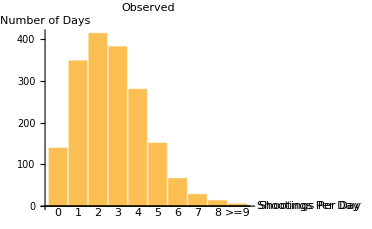

```mathematica
(*Observed Barchart*)
BarChart[{139,348,414,382,280,151,66,28,13,5},ChartLabels->{"0","1","2","3","4","5","6","7","8",">=9"},AxesLabel->{"Shootings Per Day","Number of Days"},PlotLabel->Style["Observed","Title",16]]
```

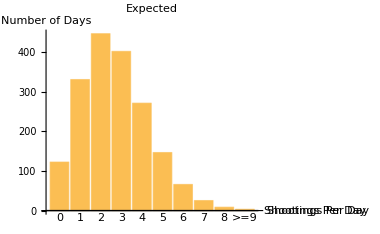

```mathematica
(*Expected Barchart*)
BarChart[{122.71,331.42,447.37,402.63,271.71,146.81,66.1,25.38,8.58,3.29},ChartLabels->{"0","1","2","3","4","5","6","7","8",">=9"},AxesLabel->{"Shootings Per Day","Number of Days"},PlotLabel->Style["Expected","Title",16]]
```

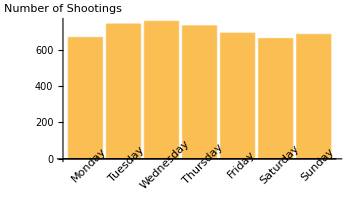

```mathematica
(*Week*)
BarChart[{668,742,757,732,692,662,685},ChartLabels->Placed[{"Monday","Tuesday","Wednesday","Thursday","Friday","Saturday","Sunday"},Axis,Rotate[#,45Degree]&],AxesLabel->Style["Number of Shootings"]]
```

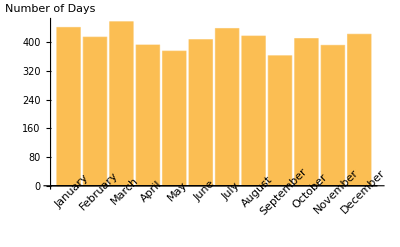

```mathematica
(*Month*)
BarChart[{442,415,458,393,376,408,439,418,363,411,392,423},ChartLabels->Placed[{"January","February","March","April","May","June","July","August","September","October","November","December"},Axis,Rotate[#,45Degree]&],AxesLabel->Style["Number of Days"]]
```